```mathematica
a[e_]:=√(M e / kT)
```

```mathematica
F[e_]:=(1+0.5/a[e]^2)Erf[a[e]]+Exp[-a[e]^2]/(a[e] √π)
```

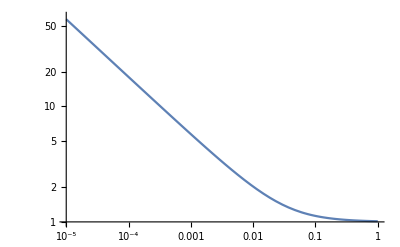

```mathematica
M=1;
kT=0.0253;
LogLogPlot[F[e],{e,1/10^5, 1},PlotRange->{1,60}]
```

```mathematica
F[1/10^5]*2.043608000000000047*10
```

1160.03

```mathematica
e0=0.01;
```

```mathematica
f[mu_,e_]:=1/(4π)√(e/e0)√(M/(2π kT 2(e+e0-2mu √(e*e0))))Exp[-M/(2 kT 2(e+e0-2mu √(e*e0)))(e0-e-(e+e0-2mu √(e*e0))/M)^2]
```

```mathematica
NIntegrate[f[mu,e],{e,0,100},{mu,-1,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.0804695

```mathematica
e0s=Table[10^i,{i, -5,1,0.02}];
```

```mathematica
integrals=Quiet@Table[e0=i;{i,8*π*NIntegrate[f[mu,e],{e,0,100},{mu,-1,1}]},{i,e0s}];
```

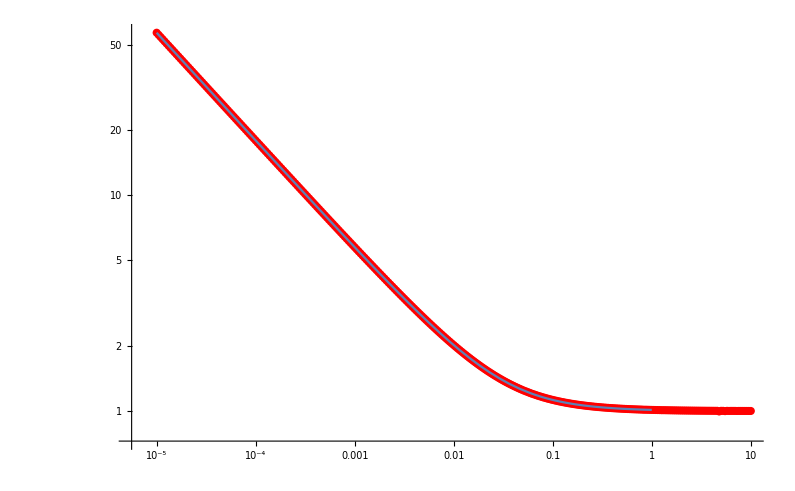

```mathematica
Show[ListLogLogPlot[integrals,PlotStyle->Red],LogLogPlot[F[e],{e,1/10^5, 1}]]
```